# Упражнения 5-6. Някои практически въпроси, свързани с интерполацията, и приложения

#### Задача 1: Да се напише функция newtonPoly[nodes_,values_,x_], която връща в нормален вид полинома на Лагранж p(x) за възлите nodes и стойности values.

```mathematica
dividedDiff[nodes_,values_]:=(
If[Length[nodes]==1,
values[[1]],
(dividedDiff[nodes[[2;;Length[nodes]]],values[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],values[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]])]
)
newtonPoly[nodes_,values_,x_]:=(
poly=0;
product=1;
For[i=1,i≤Length[nodes],i++,
poly+=dividedDiff[nodes[[1;;i]],values[[1;;i]]]*product;
product*=x-nodes[[i]]
];
poly//Expand
)
```

#### Задача 2: В таблицата са дадени данни за населението на САЩ в периода 1920-1990. Да се построи полином от седма степен, интерполиращ таблицата. Да се даде приближение на населението през 1952, 1974, 2000 година и да се сравни с действителните стойности - съответно 157млн, 214 млн, 281.42млн. година | 1920 | 1930 | 1940 | 1950 | 1960 | 1970 | 1980 | 1990 население | 106.46 | 123.08 | 132.12 | 152.27 | 180.67 | 205.05 | 227.23 | 249.46

```mathematica
nodes=Range[1920,1990,10];
values={106.46, 123.08,  132.12, 152.27,180.67, 205.05,227.23,249.46};
p[x_]:=newtonPoly[nodes,values,x];
```

```mathematica
p[1952] (*Действителната стойност за населението през 1952 е 157*)
```

157.728

```mathematica
p[1974] (*В действителност - 214*)
```

213.511

```mathematica
p[2000](*В действителност - 281.42*)
```

175.08

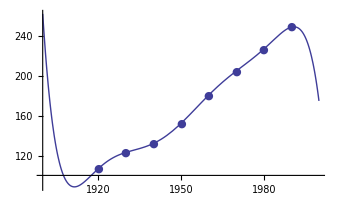

```mathematica
plot1=Plot[p[x], {x,1900,2000}]; (* Както се вижда от долната графика и от горните резултати, полиномът моделира добре изменението на населението единствено
						 в границите на интерполация - между 1920 и 1990 година*)
plot2=ListPlot[Table[{nodes[[k]],values[[k]]},{k,1,Length[nodes]}],PlotMarkers->●];
Show[plot1,plot2]
```

#### Задача 3: Да се приближи функцията f(x)=1/(1+25 x^2), като се използват полиноми от степени 10 и 4. Да се построят графиките на грешките (по абс. стойност) в двата случая

```mathematica
f[x_]:=1/(1+25 x^2)
nodes=Range[-1,1,0.2];
values=Table[f[x],{x,-1,1,0.2}];
p[x_]=newtonPoly[nodes,values,x]
Plot[{p[x],f[x]}, {x,-1,1}, PlotStyle->{{Blue, Thick}, {Red,Thick}}, PlotRange->{{-1,1},{-1,2}}]
```

1.+4.44089×10^-16 x-16.8552 x^2-2.13163×10^-14 x^3+123.36 x^4+1.24345×10^-13 x^5-381.434 x^6-1.7053×10^-13 x^7+494.91 x^8+5.68434×10^-14 x^9-220.942 x^10

При интерполиране с полиноми от висока степен можем да очакваме наличието на осцилации.Между възлите на интерполация поведението на интерполационния полином е "лошо" - виждате как в двата края на интервала грешката при апроксимация е много голяма.

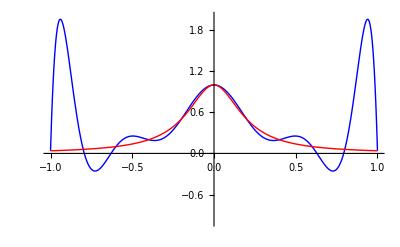

```mathematica
Plot[Abs[f[x]-p[x]],{x,-1,1},PlotRange->All]
```

Грешката е най - малка в средата на интервала. Затова, когато избираме възлите на интерполация, е добре точката, в която търсим приближената стойност да е в средата на интервала, в който интерполираме.

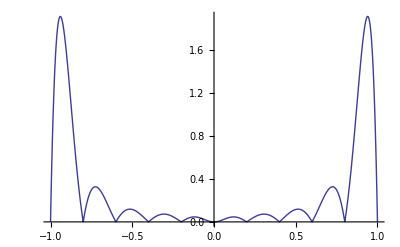

```mathematica
f[x_]:=1/(1+25 x^2)
nodes=Range[-1,1,0.5];
values=Table[f[x],{x,-1,1,0.5}];
p4[x_]=newtonPoly[nodes,values,x]
Plot[{p4[x],f[x]}, {x,-1,1}, PlotStyle->{{Blue, Thick}, {Red,Thick}}, PlotRange->{{-1,1},{-1,2}}]
```

1.-4.27719 x^2+3.31565 x^4

Приближението (като цяло) е по - добро с полинома от по - ниската степен.

1.-4.27719 x^2+3.31565 x^4

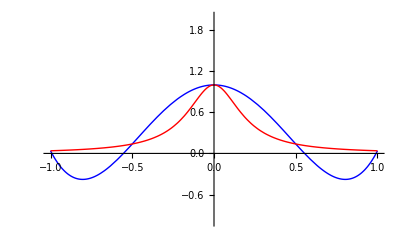

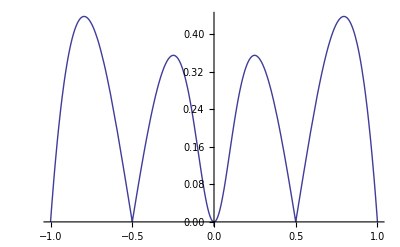

```mathematica
Plot[Abs[f[x]-p4[x]],{x,-1,1},PlotRange->All]
```

#### Задача 4: Да се състави анимация по зададените сцени:

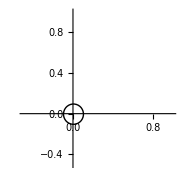
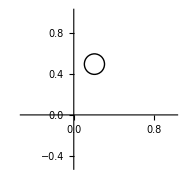
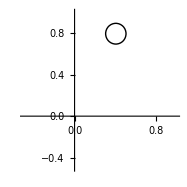

```mathematica
p[x_]=newtonPoly[{0,0.2,0.4},{0,0.5,0.8},x];
Animate[Graphics[Circle[{x,p[x]},0.1],Axes->True,
AxesOrigin->{0,0},PlotRange->{{-0.5,1},{-0.5,1}}],
  {x,0,0.4,0.01}]
```

#### Задача 5 : Проведени са експерименти, за да се определи бързодействието на един алгоритъм за сортиране в зависимост от броя елементи. Резултатите са представени в следната таблица: бр. е/ти, хил | 10 | 20 | 50 | 100 | 150 | 200 | 250 време, s | 0.1639275 | 0.53282 | 3.00007 | 11.20784 | 26.7486723 | 47.3297 | 76.80605 Да се определи колко най-много елемента могат да се сортират за не повече от 30сек.

```mathematica
p[x_]=newtonPoly[{100,150,200,250},
{11.20784,26.7486723,47.3297,76.80605},x];
Solve[p[x]==30,x]
```

{{x→47.4033-243.128 ⅈ},{x→47.4033+243.128 ⅈ},{x→159.083}}